#### Экспоненциальное сглаживание

```mathematica
passengers=Normal[ExampleData[{"Statistics","InternationalAirlinePassengers"},"TimeSeries"]];
data=passengers[[All,2]];
```

```mathematica
alpha = 0.5;
```

```mathematica
exponentialsmoothing[data_]:=Module[{},Subscript[y, 1]=data[[1]];newdata=Table[Subscript[y, t+1]=alpha*data[[t]]+(1-alpha)*Subscript[y, t],{t,1,Length@data}];
e=Length@newdata;
Do[Subscript[y, e+1]=alpha*newdata[[e]]+(1-alpha)*Subscript[y, e];newdata=Append[newdata,Subscript[y, e+1]];e=e+1,24];
ListLinePlot[{data,newdata}]]
```

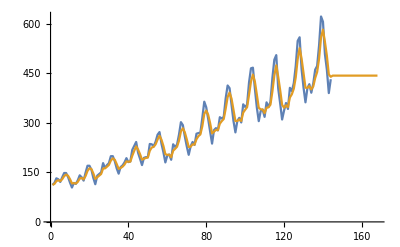

```mathematica
exponentialsmoothing[data]
```

```mathematica
alpha = 0.5;
beta=0.25;
```

```mathematica
methodHolt[data_,h_,alpha_,beta_]:=Module[{newdata={}},e=1;Subscript[te, 1]=1;Subscript[l, 1]=data[[1]];Do[Subscript[l, e+1]=alpha*data[[e]]+(1-alpha)*(Subscript[l, e]+Subscript[te, e]);Subscript[te, e+1]=beta*(Subscript[l, e+1]-Subscript[l, e])+(1-beta)*Subscript[te, e];Subscript[y, e+h]=Subscript[l, e+1]+h*Subscript[te, e+1];newdata= Append[newdata,Subscript[y, e+h]];e++,Length@data];e=Length@newdata;
Do[Subscript[l, e+1]=alpha*newdata[[e]]+(1-alpha)*(Subscript[l, e]+Subscript[te, e]);Subscript[te, e+1]=beta*(Subscript[l, e+1]-Subscript[l, e])+(1-beta)*Subscript[te, e];Subscript[y, e+h]=Subscript[l, e+1]+h*Subscript[te, e+1];newdata= Append[newdata,Subscript[y, e+h]];e++,10];
ListLinePlot[{data,newdata}]]
```

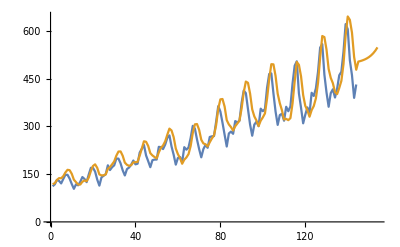

```mathematica
methodHolt[data,6,alpha=0.25,beta=0.2]
```